```mathematica
Solve[Sin[d/2]==v^2/(v^2-1),d]
```

{{d→ConditionalExpression[2 (π-ArcSin[v^2/(-1+v^2)]+2 π C[1]), C[1]∈ℤ]},{d→ConditionalExpression[2 (ArcSin[v^2/(-1+v^2)]+2 π C[1]), C[1]∈ℤ]}}

```mathematica
cotp[d_,v_]:=v^2*Cot[d/2]+Sqrt[v^4*Cot[d/2]^2+2*v^2-1]
cotm[d_,v_]:=v^2*Cot[d/2]-Sqrt[v^4*Cot[d/2]^2+2*v^2-1]
cosp[d_,v_]:=cotp[d,v]/Sqrt[1+cotp[d,v]^2]
cosm[d_,v_]:=cotm[d,v]/Sqrt[1+cotm[d,v]^2]
dcosp[d_,v_]:=(v^2 Cot[d/2]+√(-1+2 v^2+v^4 Cot[d/2]^2))/(2 v (-1+Cos[d]) √(-2+4 v^2+2 v^4 Cot[d/2]^2) (1+Cot[d/2] (v^2 Cot[d/2]+√(-1+2 v^2+v^4 Cot[d/2]^2)))^(3/2))
dcosm[d_,v_]:=-(((-v^2 Cot[d/2]+√(-1+2 v^2+v^4 Cot[d/2]^2)) Csc[d/2]^2)/(4 v √(-2+4 v^2+2 v^4 Cot[d/2]^2) (1+v^2 Cot[d/2]^2-Cot[d/2] √(-1+2 v^2+v^4 Cot[d/2]^2))^(3/2)))
Mv[d_,v_]:=Piecewise[{{-dcosp[d,v]+dcosm[d,v],d<Pi && v^2 > Tan[d/2]^2*(Csc[d/2]-1)&&v^2<1/2},{-dcosp[d,v],d>0&&v^2 >1/2},{0,d>Pi&&v^2<1/2}},0]
Mv2[d_,v_,dd_]:=Piecewise[{{(cosp[d-dd/2,v]-cosp[d+dd/2,v]-cosm[d-dd/2,v]+cosm[d+dd/2,v])/dd,d<Pi && v^2 > Tan[d/2]^2*(Csc[d/2]-1)&&v^2<1/2},{(cosp[d-dd/2,v]-cosp[d+dd/2,v])/dd,v^2 >1/2},{0,d>Pi&&v^2<1/2}},0]
```

```mathematica
FullSimplify[D[cosp[d,v],d],Assumptions->{d>0,d<2*Pi,v>0,v<1}]
```

(v^2 Cot[d/2]+√(-1+2 v^2+v^4 Cot[d/2]^2))/(2 v (-1+Cos[d]) √(-2+4 v^2+2 v^4 Cot[d/2]^2) (1+Cot[d/2] (v^2 Cot[d/2]+√(-1+2 v^2+v^4 Cot[d/2]^2)))^(3/2))

```mathematica
FullSimplify[D[cosm[d,v],d],Assumptions->{d>0,d<2*Pi,v>0,v<1}]
```

-(((-v^2 Cot[d/2]+√(-1+2 v^2+v^4 Cot[d/2]^2)) Csc[d/2]^2)/(4 v √(-2+4 v^2+2 v^4 Cot[d/2]^2) (1+v^2 Cot[d/2]^2-Cot[d/2] √(-1+2 v^2+v^4 Cot[d/2]^2))^(3/2)))

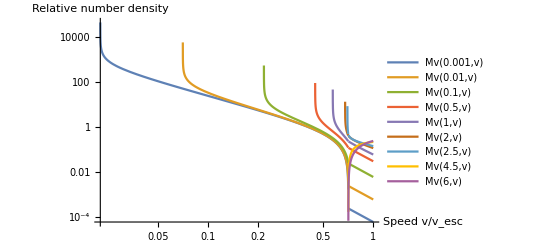

```mathematica
dist = LogLogPlot[{Mv[0.001,v],Mv[0.01,v],Mv[0.1,v],Mv[0.5,v],Mv[1,v],Mv[2,v],Mv[2.5,v],Mv[4.5,v],Mv[6,v]},{v,0.01,1},PlotRange->All,MaxRecursion->6,AxesLabel->{"Speed v/v_esc","Relative number density"},PlotLegends->"Expressions"]
```

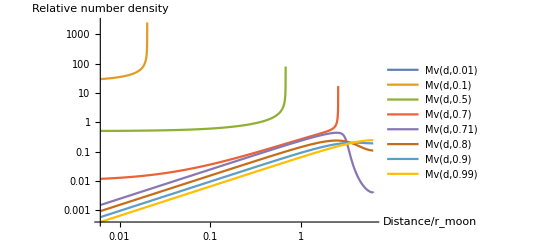

```mathematica
dist2 = LogLogPlot[{Mv[d,0.01],Mv[d,0.1],Mv[d,0.5],Mv[d,0.7],Mv[d,0.71],Mv[d,0.8],Mv[d,0.9],Mv[d,0.99]},{d,0,2*Pi},PlotRange->All,MaxRecursion->6,AxesLabel->{"Distance/r_moon","Relative number density"},PlotLegends->"Expressions"]
```

```mathematica
Manipulate[Plot[Mv[d*2*Pi,v],{d,0,1},PlotRange->All],{v,0,1}]
```

```mathematica
Export["speed_dist_2.eps",dist2]
```

speed_dist_2.eps

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["speed_dist_2.eps"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["speed_dist.eps"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["speed_dist.eps"]]]
```

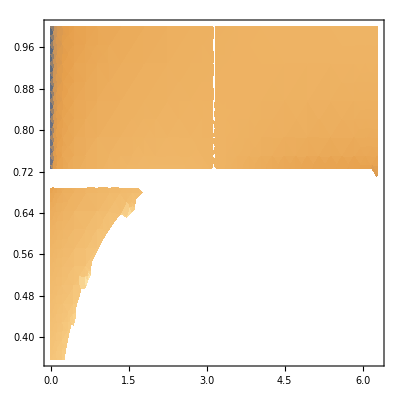

```mathematica
DensityPlot[Log10[Mv[d,v]],{d,0,2*Pi},{v,0,1},PlotRange->{-10,10}]
```

```mathematica
Manipulate[Plot[{ArcCot[-cotp[d,v]]+ArcCot[cotp[d*1.1,v]],ArcCot[-cotm[d*1.1,v]]+ArcCot[cotm[d,v]]},{v,0.01,1}],{d,0.001,2*Pi}]
```

```mathematica
D[Cot[d/2],d]
```

-1/2 Csc[d/2]^2

```mathematica
Solve[Sqrt[1+y^2]-y==x^2/y+Sqrt[x^4/y^2+2*x^2-1],y]
```

{{y→-ⅈ},{y→ⅈ},{y→-x^2/(√(1-2 x^2))},{y→x^2/(√(1-2 x^2))}}

```mathematica
Solve[x^2==y^2*(Sqrt[y^2+1]-1),y]
```

{{y→-√((2 (2/3)^(1/3) x^2)/((9 x^4+√3 √(-32 x^6+27 x^8))^(1/3))+((9 x^4+√3 √(-32 x^6+27 x^8))^(1/3))/(2^(1/3) 3^(2/3)))},{y→√((2 (2/3)^(1/3) x^2)/((9 x^4+√3 √(-32 x^6+27 x^8))^(1/3))+((9 x^4+√3 √(-32 x^6+27 x^8))^(1/3))/(2^(1/3) 3^(2/3)))},{y→-√(-((2/3)^(1/3) x^2)/((9 x^4+√3 √(-32 x^6+27 x^8))^(1/3))+(ⅈ 2^(1/3) 3^(1/6) x^2)/((9 x^4+√3 √(-32 x^6+27 x^8))^(1/3))-((9 x^4+√3 √(-32 x^6+27 x^8))^(1/3))/(2 2^(1/3) 3^(2/3))-(ⅈ (9 x^4+√3 √(-32 x^6+27 x^8))^(1/3))/(2 2^(1/3) 3^(1/6)))},{y→√(-((2/3)^(1/3) x^2)/((9 x^4+√3 √(-32 x^6+27 x^8))^(1/3))+(ⅈ 2^(1/3) 3^(1/6) x^2)/((9 x^4+√3 √(-32 x^6+27 x^8))^(1/3))-((9 x^4+√3 √(-32 x^6+27 x^8))^(1/3))/(2 2^(1/3) 3^(2/3))-(ⅈ (9 x^4+√3 √(-32 x^6+27 x^8))^(1/3))/(2 2^(1/3) 3^(1/6)))},{y→-√(-((2/3)^(1/3) x^2)/((9 x^4+√3 √(-32 x^6+27 x^8))^(1/3))-(ⅈ 2^(1/3) 3^(1/6) x^2)/((9 x^4+√3 √(-32 x^6+27 x^8))^(1/3))-((9 x^4+√3 √(-32 x^6+27 x^8))^(1/3))/(2 2^(1/3) 3^(2/3))+(ⅈ (9 x^4+√3 √(-32 x^6+27 x^8))^(1/3))/(2 2^(1/3) 3^(1/6)))},{y→√(-((2/3)^(1/3) x^2)/((9 x^4+√3 √(-32 x^6+27 x^8))^(1/3))-(ⅈ 2^(1/3) 3^(1/6) x^2)/((9 x^4+√3 √(-32 x^6+27 x^8))^(1/3))-((9 x^4+√3 √(-32 x^6+27 x^8))^(1/3))/(2 2^(1/3) 3^(2/3))+(ⅈ (9 x^4+√3 √(-32 x^6+27 x^8))^(1/3))/(2 2^(1/3) 3^(1/6)))}}

```mathematica
FullSimplify[√((2 (2/3)^(1/3) x^2)/((9 x^4+√3 √(-32 x^6+27 x^8))^(1/3))+((9 x^4+√3 √(-32 x^6+27 x^8))^(1/3))/(2^(1/3) 3^(2/3)))]
```

(√((4 3^(1/3) x^2+2^(1/3) (9 x^4+√(-96 x^6+81 x^8))^(2/3))/((9 x^4+√(-96 x^6+81 x^8))^(1/3))))/6^(1/3)

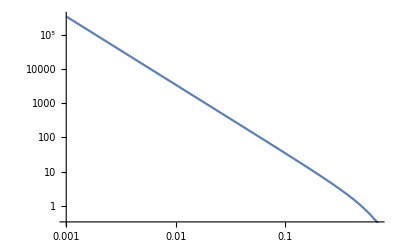

```mathematica
LogLogPlot[{-dcosp[ ArcSin[x^2/(1-x^2)],x]+dcosm[ ArcSin[x^2/(1-x^2)],x]},{x,0.001,1},PlotRange->All]
```

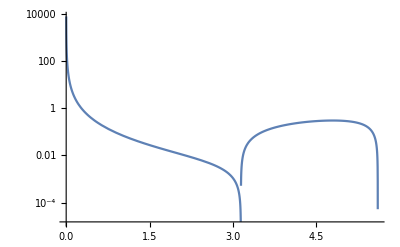

```mathematica
LogPlot[{-dcosp[ d,Sqrt[Tan[d/2]/Tan[Pi/4-d/4]]]},{d,0.001,2*Pi},PlotRange->All]
```

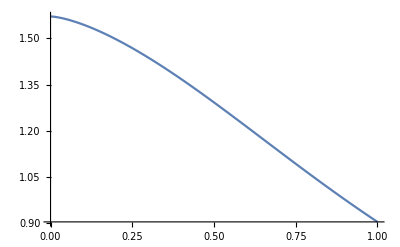

```mathematica
Plot[ArcTan[1/x^2*(√((4 3^(1/3) x^2+2^(1/3) (9 x^4+√(-96 x^6+81 x^8))^(2/3))/((9 x^4+√(-96 x^6+81 x^8))^(1/3))))/6^(1/3)],{x,0.0,1}]
```

```mathematica
FullSimplify[Solve[v^2==Tan[d/2]/Tan[Pi/4-d/4],d]]
```

{{d→ConditionalExpression[8 π C[1]+2 ⅈ Log[2]-4 ⅈ Log[-(√(1-(√((1+v^2)^2 (1+2 v^2)))/((1+v^2)^2)) ((1+2 ⅈ) v^2+(1+ⅈ) v^4+ⅈ (1+√((1+v^2)^2 (1+2 v^2)))))/(v^2+v^4)], C[1]∈ℤ]},{d→ConditionalExpression[8 π C[1]+2 ⅈ Log[2]-4 ⅈ Log[(√(1-(√((1+v^2)^2 (1+2 v^2)))/((1+v^2)^2)) ((1+2 ⅈ) v^2+(1+ⅈ) v^4+ⅈ (1+√((1+v^2)^2 (1+2 v^2)))))/(v^2+v^4)], C[1]∈ℤ]},{d→ConditionalExpression[8 π C[1]+2 ⅈ Log[2]-4 ⅈ Log[-(√(1+(√((1+v^2)^2 (1+2 v^2)))/((1+v^2)^2)) ((1+2 ⅈ) v^2+(1+ⅈ) v^4-ⅈ (-1+√((1+v^2)^2 (1+2 v^2)))))/(v^2+v^4)], C[1]∈ℤ]},{d→ConditionalExpression[8 π C[1]+2 ⅈ Log[2]-4 ⅈ Log[(√(1+(√((1+v^2)^2 (1+2 v^2)))/((1+v^2)^2)) ((1+2 ⅈ) v^2+(1+ⅈ) v^4-ⅈ (-1+√((1+v^2)^2 (1+2 v^2)))))/(v^2+v^4)], C[1]∈ℤ]}}